```mathematica
ClearAll["Global'*"];
```

```mathematica
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
```

```mathematica
(* list fonts*)
fontlist=FE`Evaluate[FEPrivate`GetPopupList["MenuListFonts"]];
```

## What is this Notebook?

This notebook produces Figure 2 of the main text, in which contact and neck heights are plotted as functions of sphere radius and Young’s modulus. 

The corresponding raw COMSOL datasets are named “06-2022-MykytkaIndrajitData” for the radius R sweep, and “13-06-2022-IndrajitsEScanData”  for the Young’s Modulus E sweep. 

The code simply reads in the raw data, makes sure everything is in SI units, and then makes the graphs found in the manuscript.

## Sphere Radius R Sweep

```mathematica
(*GLOBAL SWITCH --- ARE WE EXPORTING STUFF?*)
print=0;
```

```mathematica
(*material parameters*)
η=2 10^-5;
κ=3 10^-2;
L=2.6 10^6;
ΔT=215-100;
Π0=(κ ΔT)/L;
ρ=5 10^-1;
Subscript[ρ, l]=10^3;
(* elastic constants*)
e=50 10^3;
ν=1/2;
g=9.81;
d=3/4((1-ν^2)/e);
(* derived quantities*)
Π0=(κ ΔT η)/(L ρ);
(* Functions for non-dimensionalising, as R varies*)
F[R_]:=4/3 π Subscript[ρ, l] g R^3;
Rh[R_]:=(F[R]d R)^(1/3)
deltah[R_]:=Rh[R]^2/R;
Ph[R_]:=3/(2π)F[R]/Rh[R]^2;
lambda[R_]:=(2π)/3 Π0 F[R]^(-7/3)R^(8/3)d^(-4/3)
```

```mathematica
(* Import the data. When doing this, be careful about units! I'll convert everything to SI*)
dir=ParentDirectory[NotebookDirectory[]]<>"/06-2022-MykytkaIndrajitData/"
names={
"Data-Pressure-R0.1905mm-E50000Palambda102-extrafinemeshnew-Indrajitszie.txt"
,"Data-Pressure-R0.3240mm-E50000Palambda101-extrafinemesh-Indrajitsize.txt"
,"Data-Pressure-R0.5512mm-E50000Palambda10-0-extrafinemesh-Indrajit-size.txt"
,"Data-Pressure-R0.938mm-E50000Palambda10-1-extrafinemesh-Indrajit-size.txt"
,"Data-Pressure-R1.595mm-E50000Palambda10-2-extrafinefine-Indrajit-Sze.txt"
,"Data-Pressure-R2.714mm-E50000Palambda10-3-extrafinemesh-Indrajit-sizeexp.txt"
,"Data-Pressure-R4.617mm-E50000Palambda10-4-extrafine-Indrajit-szieexp.txt"
,"Data-Pressure-R7.855mm-E50000Palambda10-5-extremelyfinenew-Indrajit-Sze.txt"
,"profile+pressure-R13.364mm-E50000Palambda10-6-extrafinemesh.txt"
,"Pressure-R22.736mm-E50000Pa_lambda10-7extra.txt"
,"profile+pressure_R38.7mm_E50000.txt"};
Rs={0.1905,0.324,0.5512,0.938,1.595,2.714,4.617,7.855,13.364,22.736,38.7} 10^-3;
(* sanity check - do the lambdas come out right?*)
lambdasFromRs=Map[lambda,Rs];
lambdas={10^2,10^1,10^0,10^-1,10^-2,10^-3,10^-4,10^-5,10^-6,10^-7,10^-8};
lambdasFromRs/lambdas (* should all be about 1*)
```

/Users/jackbinysh/Code/SouslovLabCode/PRL2023-ModellingLeidenfrostLevitationofSoftElasticSolids/06-2022-MykytkaIndrajitData/

{0.99873,0.999919,0.999969,0.998729,1.00084,1.00004,1.00023,1.00006,0.999851,0.999767,0.997499}

```mathematica
(* DATA EXTRACTION*)
data={};
IndrajitCentreHeights={};
IndrajitNeckHeights={};
For[i=1,i≤Length[names],i++,
path=dir<>names[[i]];
tempdata= Import[path,"Table"];

(* extract the height and pressure profiles*)
(* I'm going to take everything to SI*)
tempr=tempdata[[;;,1]] 10^-3;
tempHeight=tempdata[[;;,2]] 10^-3;

(* as a little trick, I'm going to mirror the profile for negative r*)
negativer=-tempr[[2;;Length[tempr]]];
negativeHeight=tempHeight[[2;;Length[tempHeight]]];
tempr=Join[tempr,negativer];
tempHeight=Join[tempHeight,negativeHeight];

(* construct interpolating functions for the height and the pressure*)
temprtempHeight=MapThread[{#1,#2}&,{tempr,tempHeight}];
height=Interpolation[temprtempHeight];

(* now we have the interpolating function, lets get the min heights*)
innercut=0.0;
heightat0=height[innercut]; (* centre heights*)
(* the Hertzian radius is our guess at the min*)
guess=0.9Rh[Rs[[i]]];
minimavalue=First[FindMinimum[{height[r]},{r,guess}]];
(*minimaposition=(x/.Last[FindMinimum[{#[x],x>innercut},{x,0.2}]])&/@height;*)
(*minimavalue=(First[FindMinimum[{#[x],x>innercut},{x,0.2}]])&/@height; *)

(* append them to a list*)
AppendTo[IndrajitCentreHeights,heightat0];
AppendTo[IndrajitNeckHeights,minimavalue];
]
```

InterpolatingFunction::dmval: Input value {-0.0198446} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

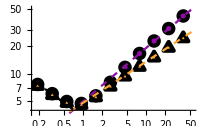

```mathematica
(* ok, make our figures*)
(* colorschemes*)
(* colourscheme, import the mpl schemes*)
(*https://mathematica.stackexchange.com/questions/127306/colormaps-for-linear-visual-perception-and-grayscale-printing*)
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
MyColorFunc=MPLColorMap["Plasma"];
MyColorFunc2=MPLColorMap["Viridis"];
(* pt to cm conversion*)
cm = 72/2.54;
(* global colour scheme for the data*)
c1=MyColorFunc[0.3];
c2=MyColorFunc[0.8];
c3=Black;
(* global font*)
myfont="Source Sans Pro";
(* tick, axis styling*)
tickthickness=0.3;
axesthickness=0.4;
(* marker styling*)
mthick=0.15;
msize=8;
m1=Graphics[{c1,EdgeForm[ Directive[Black,Thickness[mthick]] ],Disk[{0,0},1]},ImageSize->1.2msize];
m2=Graphics[{c2,EdgeForm[ Directive[Black,Thickness[ mthick]] ],Triangle[{{-1,0},{1,0},{0,Sqrt[3]}}]},ImageSize->1.3msize];
(* our centre heights*)
plt1=ListLogLogPlot[MapThread[{10^3#1,10^6#2}&,{Rs,IndrajitCentreHeights}]
,PlotMarkers->m1];
plt2=ListLogLogPlot[MapThread[{10^3#1,10^6#2}&,{Rs,IndrajitNeckHeights}]
,PlotMarkers->m2];
(* The scaling laws, with prefactors fitted*)
seventwelth=Plot[7/12 x+1.6,{x,-0.5,4}
,PlotStyle->{c1,Dashed}];
minusonehalf=Plot[-1/2 x+1.22,{x,-1.8,-0.2}
,PlotStyle->{c3,Dashed}];
fourthree=Plot[43/96 x+1.57,{x,-0.5,4}
,PlotStyle->{c2,Dashed}];
(* the final plot*)
mygraphic=Show[plt1,plt2,seventwelth,fourthree,minusonehalf
,ImageSize-> 7.2 cm
,BaseStyle->{FontFamily->myfont,FontSize->7}
,AxesStyle->Directive[Black,AbsoluteThickness[axesthickness]]
,PlotRange->All]
```

```mathematica
If[1==print,
 Export[NotebookDirectory[]<>"IndrajitsData-DimensionalHeightVsRadius.pdf",mygraphic]
]
```

### Young’s Modulus E Sweep

```mathematica
(* Note, this is just data for the centre and neck heights from Indrajit, not the full profiles*)
```

```mathematica
(* Load in Indrajit's data*)
dir=ParentDirectory[NotebookDirectory[]]<>"/13-06-2022-IndrajitsEScanData/"
Indrajithc=Import[dir<>"hcentervsE-data-plot.txt","Table"];
Indrajithc=Select[Indrajithc,Length[#]>0&];
Indrajithn=Import[dir<>"hcentervsE-data-plot.txt","Table"];
Indrajithn=Select[Indrajithn,Length[#]>0&];
```

/Users/jackbinysh/Code/SouslovLabCode/PRL2023-ModellingLeidenfrostLevitationofSoftElasticSolids/13-06-2022-IndrajitsEScanData/

```mathematica
(* ok, make our figures*)
(* ok, make our figures*)
(* colorschemes*)
(* colourscheme, import the mpl schemes*)
(*https://mathematica.stackexchange.com/questions/127306/colormaps-for-linear-visual-perception-and-grayscale-printing*)
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
MyColorFunc=MPLColorMap["Plasma"];
MyColorFunc2=MPLColorMap["Viridis"];
(* pt to cm conversion*)
cm = 72/2.54;
(* global colour scheme for the data*)
c1=MyColorFunc[0.3];
c2=MyColorFunc[0.8];
c3=Black;
(* global font*)
myfont="Source Sans Pro";
(* tick, axis styling*)
tickthickness=0.3;
axesthickness=0.4;
(* marker styling*)
mthick=0.15;
msize=5;
m1=Graphics[{c1,EdgeForm[ Directive[Black,Thickness[mthick]] ],Disk[{0,0},1]},ImageSize->1.2msize];
m2=Graphics[{c2,EdgeForm[ Directive[Black,Thickness[ mthick]] ],Triangle[{{-1,0},{1,0},{0,Sqrt[3]}}]},ImageSize->1.3msize];
(*indrajit's centre heights*)
m3=Graphics[{Blue,Opacity[0.3],RegularPolygon[4]}];
plt1=ListLogLogPlot[Indrajithc,
PlotMarkers->m1];
(* indrajit's neck heights*)
m4=Graphics[{Green,Opacity[0.3],RegularPolygon[4]}];
plt2=ListLogLogPlot[Indrajithn
,PlotMarkers->m2];
(* The scaling laws, with prefactors fitted*)
monethree=Plot[-1/3 x+7.35,{x,10.5,24},
PlotStyle->{c1,Dashed}
];
mseventwofour=Plot[-7/24 x+6.38,{x,10.5,24},
PlotStyle->{c2,Dashed}
];
hhardsphere=0.552;
hardsphereplt=Plot[ Log[ hhardsphere],{x,10,28},PlotStyle->{c3,Dashed}];

(* the final plot*)
mygraphic=Show[plt1,plt2,monethree,mseventwofour,hardsphereplt
,ImageSize-> 4.5cm
,BaseStyle->{FontFamily->myfont,FontSize->7}
,AxesStyle->Directive[Black,AbsoluteThickness[axesthickness]]
,PlotRange->All]

If[1==print,
Export[NotebookDirectory[]<>"IndrajitsData-DimensionalHeightVsModulus.pdf",mygraphic]
]
```

-Graphics-